```mathematica
Clear["Global`*"]

kHz=10^3;
GHz=10^9;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
ms=10^-3;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=970 nm;
λD2 = 852nm;780nm;
m=132.90545 amu;87amu;
ωtrap =2π 115kHz;
ΩR=2π 40kHz;3/5(2π)/(2 35us);2π 20kHz;
δ=ωtrap;+ωtrap/2(ΩR/ωtrap)^2; (*cooling is +ve*)
x0 =√(ℏ/(2 m ωtrap));
ΔkR = √2(2π)/λD2;
kOP=(2π)/λD2;
ΓOP=1/(20us);1/3 3/5(2π)/(87us);30kHz;
ηR=ΔkR x0; .22;
ηOP=kOP x0;.16;  (*need to average over 4π? also gets multiplied by nbar factor later; see above*)
nOP=1; (*avg number of OP photons scattered before spin flip. *)
```

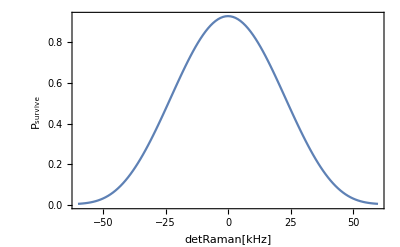

```mathematica
(*simulation params*)
Δt=5us;

α=1; (*how many pi pulses*)
tPiSqr=10us;36us; (*pi time assuming square pulse*)
doBlackman=True;

Ω0=π/(2tPiSqr);2π 254/(tPiSqr/us) kHz;
(*Δ=2π 0kHz;*)
H[t_,Δ_]:=I{{0,Ω[t]},
{Ω[t],Δ}};
Ω[t_]:=Ω0;
If[doBlackman,
tblackman=2.79 tPiSqr;
tEnd=α tblackman;
Ω[t_]:=Ω0(-1/2 Cos[2π t/tblackman]+2/25 Cos[4π t/tblackman]+21/50),
tEnd=α tPiSqr;
];
Ψ0={{1},{0}};

Clear[t,n];
t[n_]:=n Δt;
data=Reap[
Do[

Ψk=Ψ0;
n=0;

While[t[n]<tEnd,
(*RK4*)
k1=Δt H[t[n],Δ].Ψk;
k2=Δt H[t[n],Δ].(Ψk+k1/2);
k3=Δt H[t[n],Δ].(Ψk+k2/2);
k4=Δt H[t[n],Δ].(Ψk+k3);
Ψk=Ψk+1/3(k1/2+k2+k3+k4/2);
Ψk=Ψk/Norm[Ψk];
n++;
(*Sow[{n Δt/us,Abs[Ψk[[1,1]]]^2}]*)
];
Sow[{Δ/(2π kHz),Abs[Ψk[[2,1]]]^2}];
,{Δ,2π kHz Range[-60,60]}]
][[2,1]];


ListPlot[data,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"detRaman[kHz]","P_survive",ToString[α]<>"π "<>If[doBlackman,"blackman", "square"]<>" pulse"},LabelStyle->Large]
```

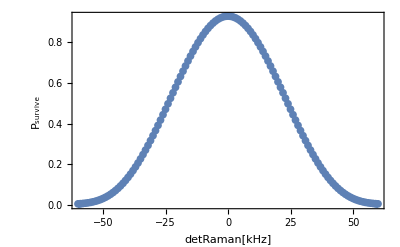

```mathematica
fitfn=A Exp[-f^2/(2 σ^2)]+offs;
nlm=NonlinearModelFit[data,fitfn,{{A,1},{σ,5},{offs}},f];
fit=nlm["BestFitParameters"];

Show[{ListPlot[data,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"detRaman[kHz]","P_survive",ToString[α]<>"π "<>If[doBlackman,"blackman", "square"]<>" pulse"},LabelStyle->Large],

Plot[fitfn/.fit,{f,-60,60}]
}]
```

```mathematica
(*some nearly conserved quantities: (for relating spectral properties to pi times*)
Ω0/(σ 2π kHz)/.fit (*1.16*)
2.355 σ kHz tPiSqr/.fit (*0.51*)
```

1.15521

0.509647

## try to fit to 2 gaussian

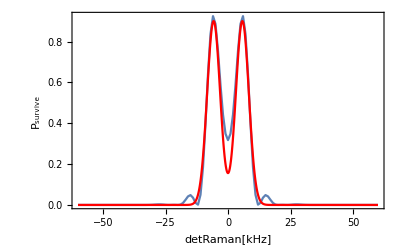

```mathematica
A=.9;
fSB = 5.75;
σ=2.6;
Show[{
ListPlot[data,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"detRaman[kHz]","P_survive",ToString[α]<>"π "<>If[doBlackman,"blackman", "square"]<>" pulse"},LabelStyle->Large],
Plot[A Exp[-(f-fSB)^2/(2 σ^2)]+A Exp[-(f+fSB)^2/(2 σ^2)],{f,-60,60},PlotRange->All,PlotStyle->Red]
}]
```

## save

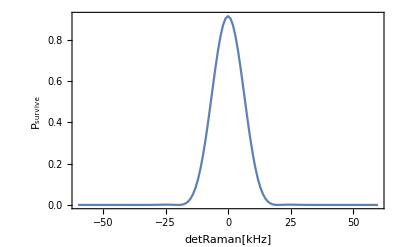

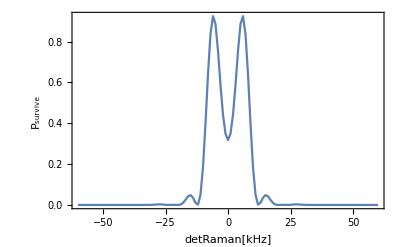

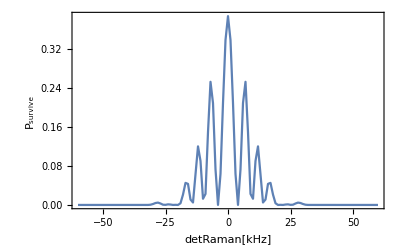

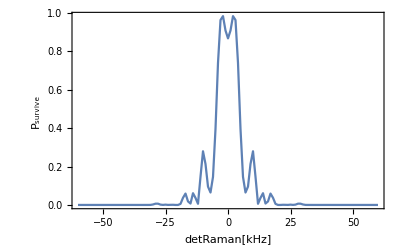

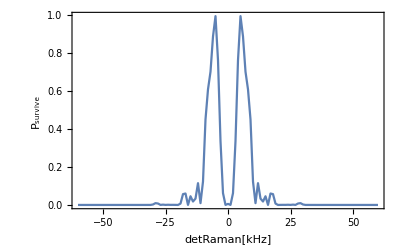

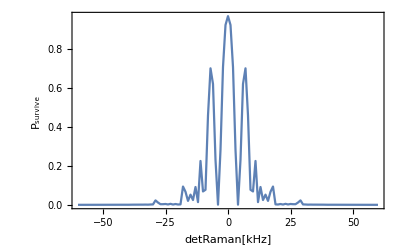

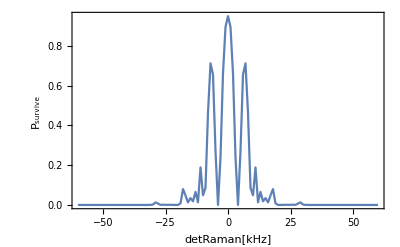

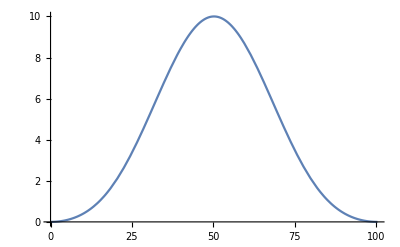

```mathematica
tRaman=2.79 36us;
tEnd=tRaman;
Ω[t_]:=Ω0(-1/2 Cos[2π t/tRaman]+2/25 Cos[4π t/tRaman]+21/50);
Plot[Ω[t us]/(2π kHz),{t,0,tRaman/us}]
```

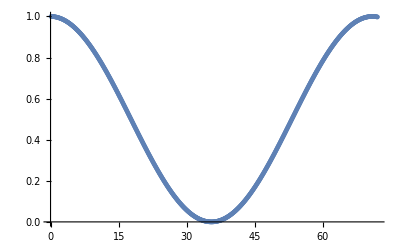

```mathematica
Ψk=Ψ0;
n=0;

Ω0=2π 254/(tEnd/us) kHz;

Δ=0;
data=Reap[
While[t[n]<2tEnd,
(*RK4*)
k1=Δt H[t[n],Δ].Ψk;
k2=Δt H[t[n],Δ].(Ψk+k1/2);
k3=Δt H[t[n],Δ].(Ψk+k2/2);
k4=Δt H[t[n],Δ].(Ψk+k3);
Ψk=Ψk+1/3(k1/2+k2+k3+k4/2);
Ψk=Ψk/Norm[Ψk];
n++;
Sow[{n Δt/us,Abs[Ψk[[1,1]]]^2}]
]][[2,1]];
ListPlot[data]
```